# IntraclassCorrelation

Find the intra-class correlation coefficient (ICC) of a list of lists

## Definition

```mathematica
IntraclassCorrelation[data_]:=Variance[Mean[#]&/@data]/(Variance[Mean[#]&/@data]+Mean[Variance[#]&/@data])//N
```

## Documentation

### Usage

IntraclassCorrelation[lst]

Returns the intra-class correlation coefficient (ICC) of the list of lists lst.

### Details & Options

The intra-class correlation is a measure of repeatability when a number of measurements are repeated over time or by different observers.

The ICC r an be calculated as the group-level variance V_G (variance in each of the subgroups) over the sum of group- and data-level (residual) variance V_R.

r=V_G/(V_G+V_R)

Low intra-class correlation indicates that the value measured within each group is not significantly correlated and therefore has low repeatability

## Examples

### Basic Examples

Calculate the repeatability of a list of three different quantities, for each of which we have 4 measurements:

```mathematica
IntraclassCorrelation[{{1,0,3,10},{100,89,102},{90,400,380}}]
```

0.679752

### Scope

An example of a data set with high intra-class correlation:

```mathematica
high=Table[#+RandomReal[{-1,1}],RandomInteger[{3,6}]]&/@RandomReal[{-3,3},20];
```

```mathematica
IntraclassCorrelation[high]
```

0.923548

A plot of the highly repeatable values:

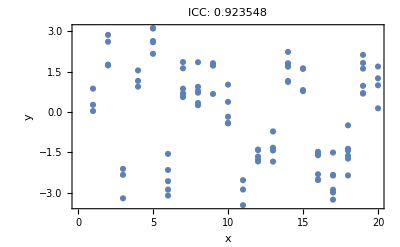

```mathematica
ListPlot[Catenate[MapIndexed[{#2[[1]],#1}&,high,{2}]],Frame->True,FrameLabel->{"x","y"},PlotLabel->StringJoin["ICC: ",ToString[IntraclassCorrelation[high]]]]
```

An example of data with low intra-class correlation:

```mathematica
low=Table[#+RandomReal[{-3,3}],RandomInteger[{3,6}]]&/@RandomReal[{-1,1},20];
```

```mathematica
IntraclassCorrelation[low]
```

0.255796

A plot of the data:

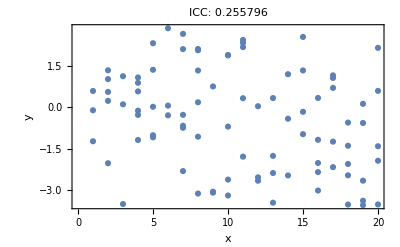

```mathematica
ListPlot[Catenate[MapIndexed[{#2[[1]],#1}&,low,{2}]],Frame->True,FrameLabel->{"x","y"},PlotLabel->StringJoin["ICC: ",ToString[IntraclassCorrelation[low]]]]
```

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Katja Della Libera

### Keywords

descriptive statistics

repeatability

grouped data

variance

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics
 Wolfram Physics Project |

### Related Symbols

Correlation

Variance

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

### Links

https://en.wikipedia.org/wiki/Intraclass_correlation

### Tests

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Greetings reviewers :)
I see there is still no statistics category :(
The difficult thing is calculating the uncertainty in ICC, I might add that later since it requires actually fitting the model this is based on and parametric bootstrapping . There's also a few older definitions of ICC (this is the Modern ICC by Ronald Fisher) that I might add in the next version.